# Variational Quantum Linear Solver

## Load Quantum Framework

Using Wolfram Quantum Framework

```mathematica
PacletInstall["https://wolfr.am/DevWQCF",ForceVersionInstall->True]
```

PacletObject[…]

```mathematica
<<Wolfram`QuantumFramework`
```

Load QuantumOptimization paclet

```mathematica
<<Wolfram`QuantumFramework`QuantumOptimization`
```

Functionalities

```mathematica
?Wolfram`QuantumFramework`QuantumOptimization`*
```

Refer to the Quantum Optimization documentation.

## Theory

The Variational Quantum Linear Solver (VQLS) is a a hybrid quantum-classical technique designed to address the Quantum Linear Systems Problem (QLSP). It aims to find linear system solutions using quantum computing techniques.

The classical problem is formulated as follows:

Given a matrix A and vector b, find x such that A.x=b

The corresponding quantum algorithm can be summarized as follows:

Given:

Problem vector: A quantum state b such that b=U0

Problem matrix: 2^n×2^n dimensional matrix A such that A=(∑_0)^(L-1)c_l A_l, where c_l ϵ ℂ  and A_l are unitary gates

We want to prepare:

A quantum state x  such that ψ=Ax  and ψ/(√ψψ)->b

### Precedents

We have this relevant first implementation of a variational quantum circuit that solves linear systems by Bravo-Prieto, you can check the paper in the following link.

#### Bravo-Prieto VQLS

First implementation of a variational quantum circuit for solving linear systems

https://quantum-journal.org/papers/q-2023-11-22-1188/pdf

Requires multiple circuits (Gates A_i and CZ_j permute):

In general the algorithm performs the calculation in a real quantum computer by obtaining multiple expected values from multiple circuit variations.

he diagram displayed is an example from one of those circuits, Gate A and the Control Z gate permute between different qubits to obtain the different expected values:

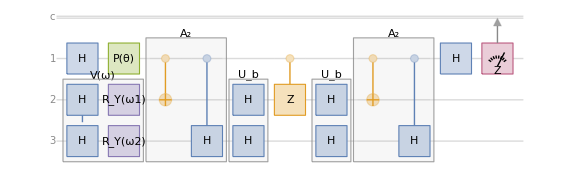

He also used a local cost function in order to avoid getting stuck in local minimum values:

C_L=1/2-1/(2n)∑_(j=0)^(n-1) (∑_(l, l') c_l c_l'^*μ_(l , l', j))/(∑_(l,l') c_l c_l'^*μ_(l , l', -1))

where μ_(l , l',j)= 0 V^†A_l'^†U Z_J U^†A_l V0, Z_-1->𝟙 and C_G->0 <->C_L->0.

You can check more about this implementation on my community post: https://community.wolfram.com/groups/-/m/t/3180154

#### Multiplexer-based VQLS

We propose a Multiplexer–Based Variational Quantum Linear Solver (MB-VQLS). The primary distinctions between MB–VQLS and a conventional VQLS lie in two key aspects:

The controlled implementation of the matrix A through a multiplexer

Quantum fidelity cost function:

f(ω)=1- |bψ(ω),|,^2

The solution to the linear system is encoded directly in the amplitudes of the resultant quantum state.

Further steps will show that we can avoid some b and A restrictions using their normalization terms. This would help us find solutions for any system.

### A.x Operation Circuit Representation

Considering an n×n A matrix and an n-element vector x, we look to compute the operation A.x with a quantum circuit using A as a controlled operation.

To start, let’s define a complex vector x using RandomComplex, and a random real matrix A called “a”:

```mathematica
x=RandomComplex[{-1-1*I,+1+1*I},4]
```

{-0.126112-0.770322 ⅈ,0.302431-0.0695352 ⅈ,0.0386691-0.00105955 ⅈ,0.0950529-0.0692226 ⅈ}

We will begin the implementation by encoding the matrix A into the quantum circuit:

```mathematica
a=RandomReal[{-1,1},{4,4}];
a//MatrixForm
```

(0.25529 | 0.831537 | 0.774413 | 0.967247
0.345805 | 0.29044 | 0.424374 | -0.428653
-0.406224 | 0.260866 | -0.687513 | 0.829075
-0.901911 | 0.438124 | -0.841926 | -0.108815)

We proceed to generate a quantum operator A and decompose it in Pauli matrices such that A=∑c_j A_j:

```mathematica
A=QuantumOperator[a];
```

```mathematica
pauliDecompose=A["PauliDecompose"]
```

<|XX→0.187644+0. ⅈ,XY→0.+0.426412 ⅈ,XZ→0.0896794+0. ⅈ,XI→0.0944149+0. ⅈ,YX→0.+0.508167 ⅈ,YY→0.154976+0. ⅈ,YZ→0.+0.511854 ⅈ,YI→0.+0.078465 ⅈ,ZX→0.297548+0. ⅈ,ZY→0.-0.296318 ⅈ,ZZ→0.135887+0. ⅈ,ZI→0.335515+0. ⅈ,IX→0.291123+0. ⅈ,IY→0.+0.539183 ⅈ,IZ→-0.153462+0. ⅈ,II→-0.0626495+0. ⅈ|>

In order to implement the controlled A gates, we will turn the Pauli matrices as targets into a multiplexer, and the controlled qubits would be evaluated by a √c state:

```mathematica
multiplexer=QuantumCircuitOperator["Multiplexer"@@Keys[pauliDecompose]];
```

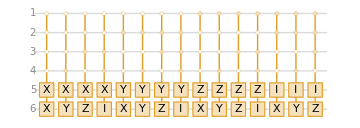

```mathematica
multiplexer["Diagram"]
```

```mathematica
ancillary=QuantumState[Sqrt@Values[pauliDecompose],"Label"->"√c"];
```

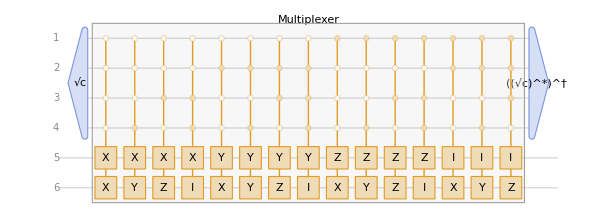

```mathematica
QuantumCircuitOperator[{
ancillary,
multiplexer,
SuperDagger[ancillary["Conjugate"]]
}]["Diagram"]
```

Finally, we would let our vector x be evaluated by the multiplexer in our circuit:

```mathematica
productCircuit=QuantumCircuitOperator[{
ancillary,
QuantumState[x,"Label"->"x"]->{5,6},
multiplexer,
SuperDagger[ancillary["Conjugate"]]
}];
```

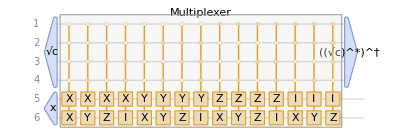

```mathematica
productCircuit["Diagram",ImageSize->Full]
```

Evaluate our circuit and check the amplitudes of the resultant state:

```mathematica
productCircuit[]
```

QuantumState[…]

```mathematica
productCircuit["Table"]
```

| 1
00 | 0.341173-0.322253 ⅈ
01 | 0.0198934-0.257354 ⅈ
10 | 0.182344+0.238122 ⅈ
11 | 0.203345+0.672721 ⅈ

The result corresponds to the equivalent classical operation:

```mathematica
a.x
```

{0.341173-0.322253 ⅈ,0.0198934-0.257354 ⅈ,0.182344+0.238122 ⅈ,0.203345+0.672721 ⅈ}

## Quantum Linear Solver Implementation

Now that we learned how to compute the product of a matrix and vector using a quantum circuit, we have a better understanding of how to implement our new variational quantum linear solver.

Given a b problem vector and an A problem matrix, the basic steps are:

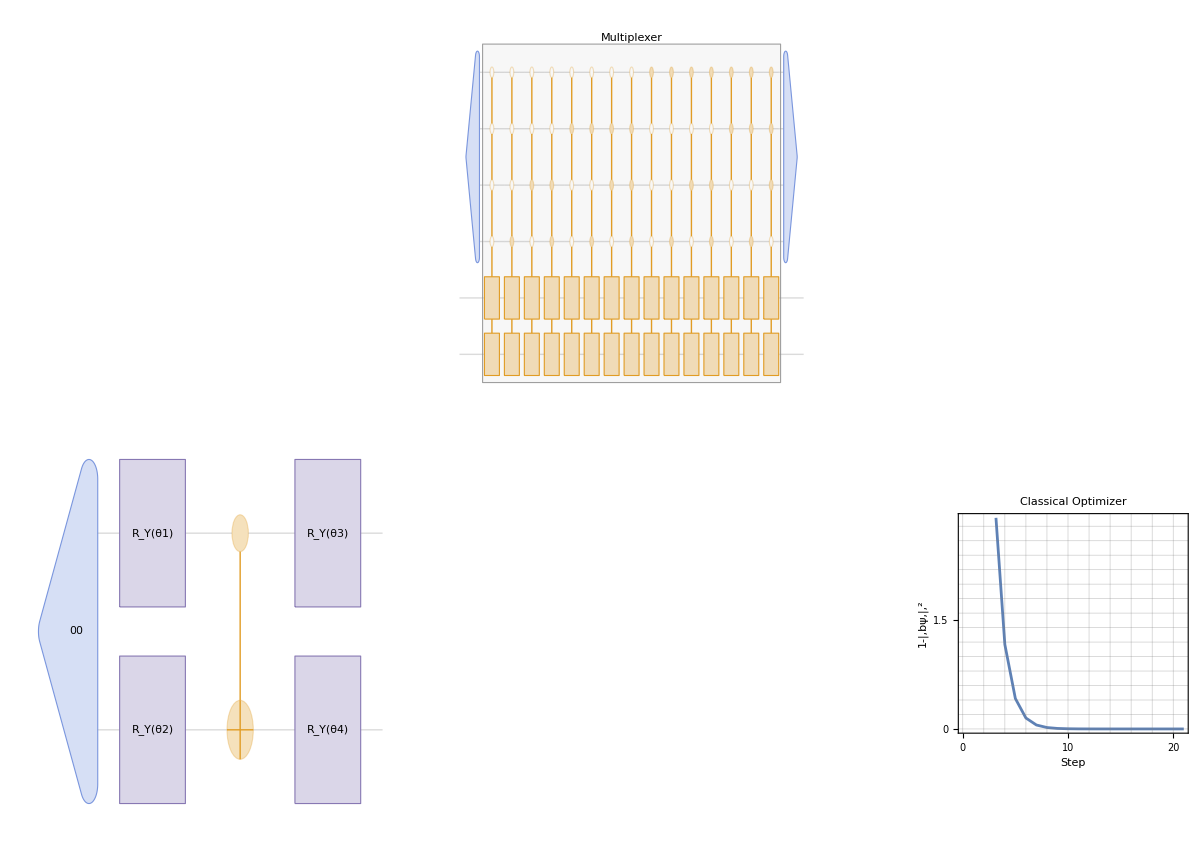

#### Initial problem setup

In order to implement this algorithm, we will start coding a simple example using a random vector b and a random A matrix:

```mathematica
matrixA=RandomReal[{0,1},{4,4}];
```

```mathematica
matrixA//MatrixForm
```

(0.909708 | 0.494552 | 0.49149 | 0.862494
0.724248 | 0.484333 | 0.413379 | 0.721778
0.128352 | 0.905764 | 0.193863 | 0.0352042
0.509416 | 0.602268 | 0.0978288 | 0.510178)

```mathematica
vectorb=RandomReal[{-0.1,+0.1},4]
```

{0.0695503,-0.0689988,0.0678855,0.0997898}

As we previously discussed, we need to save the normalization terms, since we will be working with the normalized matrix and vector:

```mathematica
normA=Norm[matrixA];
normb=Norm[vectorb];
```

In later steps, we will refer to b̂ and Â as the normalized vector b and matrix A, respectively. Then the solution for the Â and b̂ problem would be called x^(^\b)(θ_opt). Applying b and A normalization terms will help us recover the original A.x(θ_opt)=b solution.

#### Multiplexer implementation

For this section, we need to repeat what is stated in the A.x Operation Circuit Representation section.

First, we need to decompose Â in Pauli matrices such that Â=∑c_i A_i:

```mathematica
pauliDecompose=QuantumOperator[matrixA/normA]["PauliDecompose"];
```

```mathematica
pauliDecompose
```

<|XX→0.312427+0. ⅈ,XY→0.+0.098157 ⅈ,XZ→-0.081757+0. ⅈ,XI→0.225682+0. ⅈ,YX→0.-0.0161733 ⅈ,YY→-0.00612614+0. ⅈ,YZ→0.+0.0282848 ⅈ,YI→0.+0.0560347 ⅈ,ZX→0.126056+0. ⅈ,ZY→0.-0.0193967 ⅈ,ZZ→0.0861091+0. ⅈ,ZI→0.0801079+0. ⅈ,IX→0.156946+0. ⅈ,IY→0.-0.033938 ⅈ,IZ→0.0126617+0. ⅈ,II→0.243584+0. ⅈ|>

Next, implement the multiplexer:

```mathematica
multiplexer=QuantumCircuitOperator["Multiplexer"@@Keys[pauliDecompose]];
```

```mathematica
ancillary=QuantumState[Sqrt@Values[pauliDecompose],"Label"->"√c"];
```

We obtain the first section of the variational circuit for the VQLS:

```mathematica
qlscircuit=QuantumCircuitOperator[{
ancillary,
multiplexer,
SuperDagger[(ancillary["Conjugate"])]
}];
```

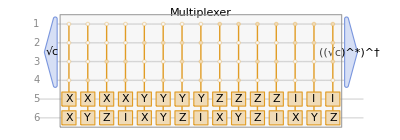

```mathematica
qlscircuit["Diagram",ImageSize->Full]
```

#### General symbolic ansatz

Define a general state ansatz for 4-qubits with real amplitudes. Remember we are working with x̂(ω) instead of x(ω); label it so we do not forget about it:

```mathematica
parameters=GenerateParameters[1,4];
ansatz=QuantumState[parameters,"Label"->"x̂(θ)","Parameters"->parameters];
```

```mathematica
ansatz["Formula"]
```

θ100+θ201+θ310+θ411

Finally, we implement the circuit and the correspondent state:

```mathematica
vqlscircuit=qlscircuit[QuantumOperator[ansatz->{5,6}]];
```

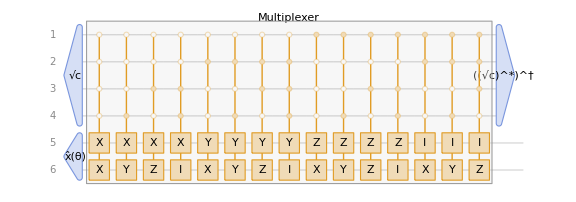

```mathematica
vqlscircuit["Diagram",ImageSize->Large]
```

Wolfram Quantum Framework quantum states (and measurements) keep the parameters defined in previously used circuits, so it would be optimum to work with the resultant state:

```mathematica
ψ=vqlscircuit[]
```

QuantumState[…]

We can perform a first test to obtain ψ(ω_init)=Â.x̂(θ_init):

```mathematica
init=Normalize[0.01*RandomVariate[NormalDistribution[],4]]
```

{0.264994,-0.411396,-0.784879,-0.380126}

```mathematica
ψ[AssociationThread[parameters->init]]["Table"]
```

| 1
00 | -0.313933+0. ⅈ
01 | -0.281493+0. ⅈ
10 | -0.234128+0. ⅈ
11 | -0.178093+0. ⅈ

As we can see, it is not close enough to b̂ in order to call it a good approximation:

```mathematica
QuantumState[vectorb/normb]["Table"]
```

| 1
00 | 0.447414
01 | -0.443866
10 | 0.436705
11 | 0.641944

#### Optimization

We are recovering our results from states’ amplitudes and there are some considerations to take into account. The cost function f(θ) we defined previously depends heavily on the quantum fidelity from the b and ψ states:

f(θ)=0↔ℱ=|bψ(θ_opt)|,^2=1

The cost function minimization ensures that the probability distributions of b and ψ are identical, such that:

ψ(θ_opt)=ⅇ^ⅈϕ b

In other words, this cost function does not ensure that the amplitudes of both states are identical, but rather that they are proportional by a global phase:

ψ=∑α_i i &b=∑β_i i ->α_i=ⅇ^ⅈϕ β_i

In order to correct our result, we need to find the global phase and apply it along with the normalization terms for both b and A once our calculation is done, such that:

x_sol=1/ⅇ^ⅈϕ(||b||)/(||A||)x(θ_opt)

Implement the cost functions previously defined, rememer to use the normalized vector b:

```mathematica
qb=QuantumState[vectorb/normb]["Normalize"];
```

```mathematica
fidelity[v1_,v2_,v3_,v4_]:=QuantumDistance[qb,ψ[v1,v2,v3,v4]["Normalize"],"Fidelity"];
```

Now, let’s optimize the cost function using FindMinimum, with our initial guess as the starting point:

```mathematica
ip=Thread[{parameters,init}];
optFM=FindMinimum[fidelity[θ1,θ2,θ3,θ4],ip];//Quiet
```

```mathematica
optFM
```

{0.180515,{θ1→-1.31557×10^10,θ2→-2.58751×10^9,θ3→1.14111×10^10,θ4→8.36485×10^9}}

As we can see, FindMinimum is having some difficulty finding the minimal value, so we might switch to NMinimize, which will return a value for the cost function that is very close to zero:

```mathematica
optNM=NMinimize[fidelity[θ1,θ2,θ3,θ4],{θ1,θ2,θ3,θ4}];
```

```mathematica
optNM
```

{1.42109×10^-14,{θ1→2.73792×10^9,θ2→-6.78883×10^7,θ3→-7.73907×10^8,θ4→-2.33952×10^9}}

Let’s compare the probability distribution of ψ(θ) and b probability distributions:

```mathematica
Dataset[<|"ψ"->ψ[<|Last[optNM]|>]["Probabilities"],"b"->QuantumState[vectorb/normb]["Probabilities"]|>]//Transpose
```

As we can notice, the values are quite close! However, as mentioned earlier, while the probability distributions match, the amplitudes do not necessarily align:

```mathematica
Dataset[<|"ψ"->ψ[<|Last[optNM]|>]["Amplitudes"],"b"->QuantumState[vectorb/normb]["Amplitudes"]|>]//Transpose
```

This is basically is saying that we found ψ(θ_opt)=ⅇ^ⅈϕ b̂:

```mathematica
optψ=ψ[<|Last@optNM|>]["AmplitudesList"]
```

{2.73736×10^7+0. ⅈ,-2.71565×10^7+0. ⅈ,2.67183×10^7+0. ⅈ,3.92752×10^7+0. ⅈ}

The following step is to obtain the global phase ⅇ^ⅈϕ. We can check that it is the same for each amplitude:

```mathematica
globalphase=optψ/(vectorb/normb)
```

{6.11817×10^7+0. ⅈ,6.11817×10^7+0. ⅈ,6.11817×10^7+0. ⅈ,6.11817×10^7+0. ⅈ}

We can verify 1/ⅇ^ⅈϕ ψ(ω_opt)=b̂ using the mean value of the global phase:

```mathematica
1/Mean[globalphase]*optψ-qb["AmplitudesList"]//Chop
```

{-1.26408×10^-7,7.94917×10^-8,6.21723×10^-8,2.04941×10^-7}

Calculate x̂(θ_opt):

```mathematica
optX=ansatz[<|Last@optNM|>]["AmplitudesList"]
```

{2.73792×10^9,-6.78883×10^7,-7.73907×10^8,-2.33952×10^9}

Now recover x(ω_opt) by applying the global phase and normalization terms: x(ω_opt)=1/ⅇ^iϕ(||b||)/(||A||)x̂(ω_opt):

```mathematica
1/Mean[globalphase]*normb/normA*optX//Chop
```

{3.23053,-0.0801031,-0.913152,-2.76045}

We can verify our result:

```mathematica
LinearSolve[matrixA,vectorb]
```

{3.23053,-0.0801031,-0.913152,-2.76045}

```mathematica
%%-%//Abs
```

{6.29597×10^-7,7.79645×10^-8,6.58594×10^-9,6.00327×10^-7}

#### Optimization using quantum natural gradient descent

As explained in a previous example, we can optimize using QuantumNaturalGradientDescent, calculating their correspondent Fubini–Study metric tensor.

A useful question to consider is: “Which state are we using in the Fubini-Study metric tensor function?” In this context, the ansatz does not capture the full geometry of the problem, so the most appropriate choice is the variational state ψ, which is parameterized and encodes the essential information about the system.

```mathematica
fubini=FubiniStudyMetricTensor[ψ];
```

Let’s try with a pair of steps on the optimizer with η->0.6:

```mathematica
opt=GradientDescent[fidelity,init,"LearningRate"->0.6,"MaxIterations"->2];
```

```mathematica
qopt=QuantumNaturalGradientDescent[fidelity,fubini,"InitialPoint"->init,"LearningRate"->0.6,"MaxIterations"->2];
```

The result is quite remarkable: the Quantum Natural Gradient Descent outperforms regular gradient descent and reaches the minimum value in only two steps!

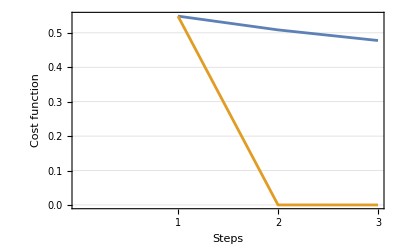

```mathematica
ListLinePlot[{fidelity@@@opt,fidelity@@@qopt},
Frame->True,FrameLabel->{"Steps","Cost function"},
GridLines->Automatic,FrameTicks->{Automatic,{Range[3],None}}]
```

We can verify that the minimization approaches to 0:

```mathematica
fidelity@@@qopt//Last
```

0.0000146428

Checkψ(θ) and b probability distributions:

```mathematica
association=AssociationThread[parameters,Last@qopt];
```

```mathematica
Dataset[<|"ψ"->ψ[association]["Probabilities"],"b"->QuantumState[vectorb/normb]["Probabilities"]|>]//Transpose
```

As you may have noticed, the probabilities match, but with less precision in this case. However, the amplitudes are completely different, and they even have different signs!

```mathematica
Dataset[<|"ψ"->ψ[association]["Amplitudes"],"b"->QuantumState[vectorb/normb]["Amplitudes"]|>]//Transpose
```

This is basically is saying that we found ψ(θ_opt)=ⅇ^ⅈϕ b̂:

```mathematica
optψ=ψ[association]["AmplitudesList"]
```

{-0.516727+0. ⅈ,0.520752+0. ⅈ,-0.505349+0. ⅈ,-0.745124+0. ⅈ}

The following step is to obtain the global phase ⅇ^ⅈϕ:

```mathematica
globalphase=optψ/(vectorb/normb)
```

{-1.15492+0. ⅈ,-1.17322+0. ⅈ,-1.15719+0. ⅈ,-1.16073+0. ⅈ}

Now, during the process of obtaining the global phase, we observe that the values are not exactly the same. In this case, when we use the mean value of the global phase, we can check that the deviation is small enough for the desired precision.

Calculate x(θ_opt):

```mathematica
optX=ansatz[association]["AmplitudesList"]
```

{-52.117+0. ⅈ,1.29782+0. ⅈ,14.7413+0. ⅈ,44.5355+0. ⅈ}

Now recover x(ω_opt) by applying the global phase and normalization terms x(ω_opt)=1/ⅇ^iϕ(||b||)/(||A||)x̂(ω_opt):

```mathematica
1/Mean[globalphase]*normb/normA*optX//Chop
```

{3.23915,-0.0806614,-0.916192,-2.76794}

We can verify our result approximation:

```mathematica
LinearSolve[matrixA,vectorb]
```

{3.23053,-0.0801031,-0.913152,-2.76045}

```mathematica
%%-%//Abs
```

{0.00861713,0.000558259,0.00304054,0.00749401}

After repeating all the same steps from the previous example, we get a final result that is close to the true result but with slightly less precision. What’s remarkable about this solution is that we achieved it in only two steps! Of course, the results depend heavily on the learning rate eta, so it’s important to fine-tune it to ensure that the optimization is done efficiently.